# Direction Fields Assignment

### Instructions

The purpose of this assignment is to assess your ability to use VectorPlot command to visualize differential equations in Mathematica. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF.
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

### Problem 1

Find the solution for each of the following initial value problems and store your solution to a function. (use your first name as the name of the function in part a and use your last name as the name of the function in part b) 
1. Plot the direction field and the solution together for each of the problems to verify that you have the correct solution. Plot with a range of x values {x,-4,4} and a range of y values {y,-8,8}.

a)  dy/dx=x^2 y subject to y(1)=3

```mathematica
calebSoln[x_]=y[x]/.DSolve[{y'[x]==x^2 y[x],y[1]==3},y[x],x];
calebSlope=VectorPlot[{1,x^2 y},{x,-1,1},{y,-1,3},VectorScale->{.03,.01,None},VectorPoints->20];
```

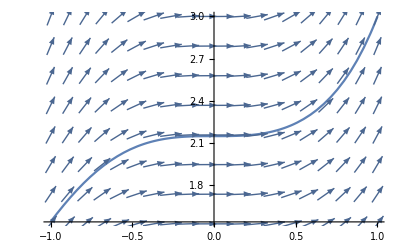

```mathematica
Show[Plot[calebSoln[x],{x,-1,1}],calebSlope]
```

b)  dy/dx=4 x^2+7y subject to y(2)=1

```mathematica
jacobsSoln[x_]=y[x]/.DSolve[{y'[x]==4 x^2+7y[x],y[2]==1},y[x],x];
jacobsSlope=VectorPlot[{1,4 x^2+7y},{x,-1,1},{y,-1,3},VectorScale->{.01,.01,None},VectorPoints->50];
```

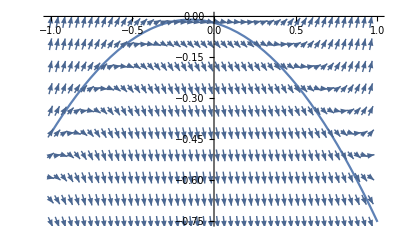

```mathematica
Show[Plot[jacobsSoln[x],{x,-1,1}],jacobsSlope]
```

### Problem 2

Plot the direction field for the differential equation dy/dx=(4-y)(1+y) . Describe the long term behavior (i.e. what happens to the solution as x→∞) for a solution that satisfies each of the following initial conditions.

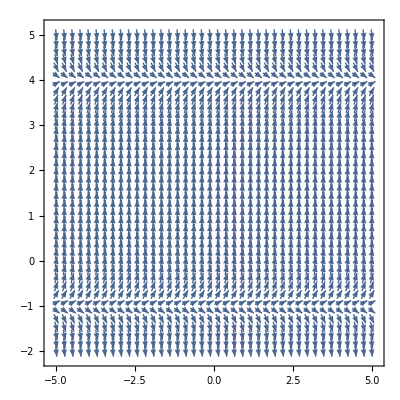

```mathematica
VectorPlot[{1,(4-y)(1+y)},{x,-5,5},{y,-2,5},VectorScale->{.02,.2,None},VectorPoints->40]
```

a) Describe the long term behavior for the solution that satisfies y(0)=-1.

The solution to the differential equation as x→∞ would approach y=4

b) Describe the long term behavior for the solution that satisfies y(0)=4.

The solution to the differential equation as x→∞ produce a linear equation y=4

c) Describe the long term behavior for the solution that satisfies y(0)=-2.

The solution to the differential equation as x→∞ would go to -∞

d) Describe the long term behavior for the solution that satisfies y(0)=5.

The solution to the differential equation as x→∞ would approach y=4